```mathematica
lsEigenvalue[H_]:=Module[{emax,emaxspace,emin,eminspace,es},(*Find the largest and smallest eigenvalue of a Hermitian matrix H together with the corresponding eigenspace (naive implementation)*)es=Sort[Eigenvalues[H],Re[#1]<Re[#2]&];
emin=First[es];
emax=Last[es];
eminspace=Orthogonalize[NullSpace[H-emin*IdentityMatrix[Length[H]]]];
emaxspace=Orthogonalize[NullSpace[H-emax*IdentityMatrix[Length[H]]]];
Return[{{emin,eminspace},{emax,emaxspace}}]]

plotNR[A_,n_]:=Module[{t=0.,td=2 π/n,Ht,Kt,points={},segments={},emax,emaxspace,emin,eminspace,vp,vm,Q,R},PrintTemporary[ProgressIndicator[Dynamic[t],{0,2 π}]];
(*data for numeric range plot*)While[t<2 π,Ht=(Exp[-I t]*A+Exp[I t]*ConjugateTranspose[A])/2;
{emax,emaxspace}=Last[lsEigenvalue[Ht]];
Which[(*One dimensional eigenspace*)Length[emaxspace]==1,vp=First[emaxspace];
AppendTo[points,Conjugate[vp].A.vp],(*Two or greater dimension-- almost does not happen?*)Length[emaxspace]>1,Kt=(Exp[-I t]*A-Exp[I t]*ConjugateTranspose[A])/(2 I);
Q=Transpose[emaxspace];
R=ConjugateTranspose[Q].Kt.Q;
{{emin,eminspace},{emax,emaxspace}}=lsEigenvalue[R];
vp=Q.First[emaxspace];
vm=Q.First[eminspace];
AppendTo[segments,{Conjugate[vm].A.vm,Conjugate[vp].A.vp}],(*Fail*)True,Print["Error"]];
t=t+td;];
Return[{DeleteDuplicates[points],DeleteDuplicates[segments]}]]
```

(1+ⅈ | 7+ⅈ
7 | ⅈ)

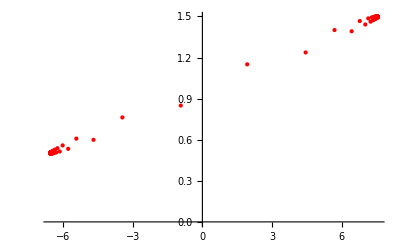

```mathematica
A = {{I +1,7 + I},{1 + 6,I}}
ListPlot[plotNR[A, 1000][[1]]/.{Complex[x_,y_]->{x,y}, x_Real->{x,0}}, PlotStyle->Directive[Red,PointSize[Medium]]]
```

```mathematica
fval[mat_?SquareMatrixQ,t_?NumericQ]/;Internal`EffectivePrecision[mat]<∞||InexactNumberQ[t]:=Module[{tm,v},tm=(#+ConjugateTranspose[#])/2&[mat Exp[I t]];
v=Quiet[Check[First[Eigenvectors[tm,1,Method->{"Arnoldi","Criteria"->"RealPart"}]],MaximalBy[Transpose[Eigensystem[tm]],First][[1,-1]],Eigenvectors::arall]];
(Conjugate[v].mat.v)/(Conjugate[v].v)]
```

```mathematica
grcar[r:_Integer?Positive:3,n_Integer?Positive]:=SparseArray[{{j_,k_}/;j==k+1:>-1,{j_,k_}/;0≤k-j≤r:>1},{n,n}]
```

```mathematica
mat=grcar[32]
```

SparseArray[…]

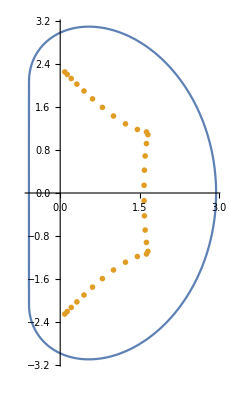

```mathematica
ParametricPlot[ReIm[fval[mat,t]],{t,0,2 π},Epilog->{AbsolutePointSize[4],ColorData[97,2],Point[ReIm[eigs]]}]
```